```mathematica
SetDirectory[NotebookDirectory[]];
```

# Pre

```mathematica
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ=75.8;
ν=-482.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=300;
```

# Mean-field effective potential

## effective potential

92.325526

135.695

480.438

300.058

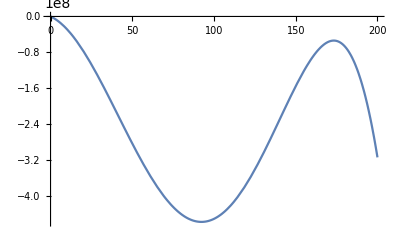

```mathematica
a=FindMinimum[{V[a1^2/2,h,1,0.,λ,ν,c]+Vvacuum[a1^2/2,h,M1],0<a1<195},{a1,90},WorkingPrecision->8][[2]][[1]][[2]]//Quiet

√Vd1rhovacuum[a^2/2,h,λ,ν,M1]
√(Vd1rhovacuum[a^2/2,h,λ,ν,M1]+2*a^2/2*Vd2rhovacuum[a^2/2,h,λ,ν,M1])
√mf2[h,a^2/2]
Plot[{V[a^2/2,h,1,0,λ,ν,c]+Vvacuum[a^2/2,h,M1]},{a,0,200},PlotRange->All]
(*Zps[a^2/2,h,1.,0.,400]*)
```

```mathematica
(*fpi=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,μ,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];*)
```

```mathematica
ListPlot[fpi,PlotRange->All]
```

ListPlot::lpn: fpi 不是由数字或者数对组成的列表.

ListPlot[fpi,PlotRange→All]

# Mean-field wave function renormalization

## threshold functions and equations

```mathematica
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,h,T,μ]+2/3 F3[q,ρ,h,T,μ]),{q,0.,500.,20000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

## σ data at μ=0

```mathematica
fpimu0=Table[Flatten[ParallelTable[{FindMinimum[{V[a^2/2,h,i*10.,j*5.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,10},AccuracyGoal->5,PrecisionGoal->5][[2]][[1]][[2]]//Quiet},{i,1,1000}]],{j,0,0}];
```

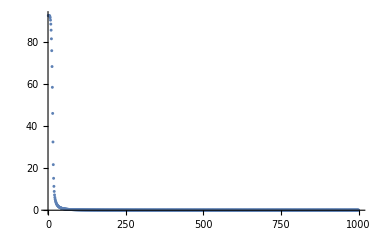

```mathematica
ListPlot[fpimu0,PlotRange->All]
```

## Z_π(p=0)

### M=300

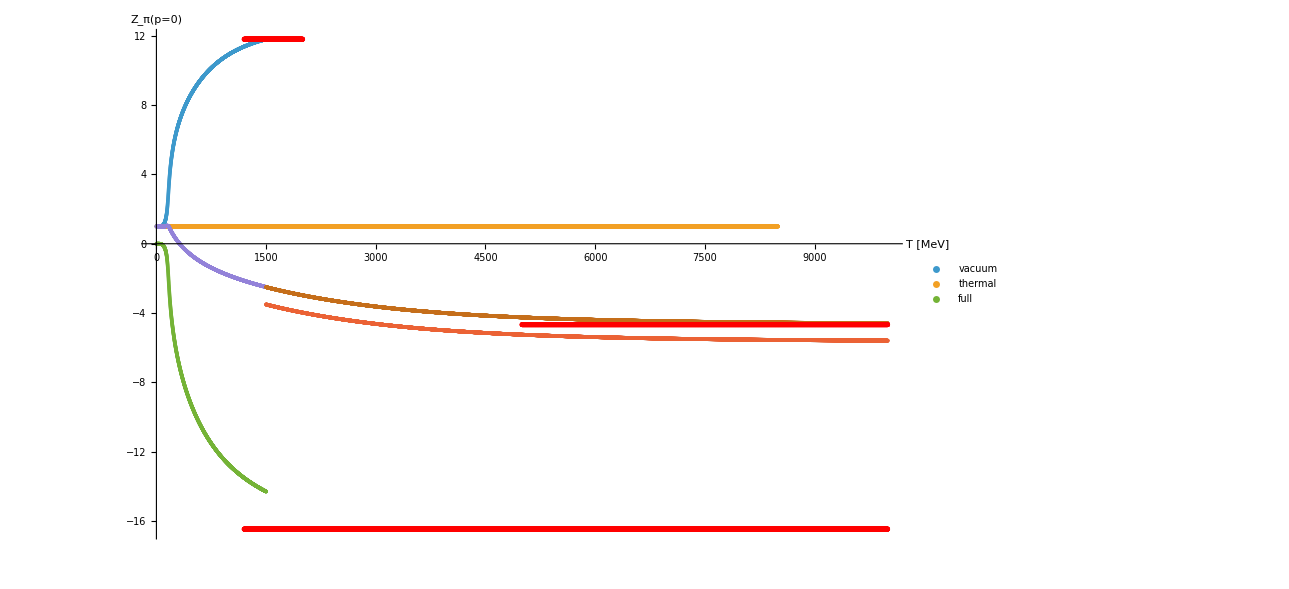

```mathematica
Zpsvac1[ρ_,h_,T_,μ_,M_]:=Zpsvac[ρ,h,M]+1.;
Zpsthr1[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ];
Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
Zvac=Flatten[ParallelTable[Zpsvac1[(fpimu0[[1]][[i]])^2/2,h,N[i],0.,300.]//Quiet,{i,1,1500}]];
Zvac2=Flatten[ParallelTable[Zpsvac1[(fpimu0[[1]][[l]])^2/2,h,N[i],0.,300.]//Quiet,{i,1500,10000}]];
Zthr=Flatten[ParallelTable[Zpsthr1[(fpimu0[[1]][[i]])^2/2,h,N[i],0.,300.]//Quiet,{i,1,1500}]];
Zthr2=Flatten[ParallelTable[{i,Zpsthr1[(fpimu0[[1]][[l]])^2/2,h,N[i],0.,300.]//Quiet},{i,1500,10000}],0];
Zall=Flatten[ParallelTable[{i,Zps[(fpimu0[[1]][[i]])^2/2,h,N[i],0.,300.]//Quiet},{i,1,1500}],0];
Zall2=Flatten[ParallelTable[{i,Zps[(fpimu0[[1]][[l]])^2/2,h,N[i],0.,300.]//Quiet},{i,1500,10000}],0];
Λ=10000.;
l=Length[fpimu0[[1]]];
ZplotM300=Show[ListPlot[{Zvac,Zvac2,Zthr,Zthr2,Zall,Zall2},AxesLabel->{"T [MeV]","Z_π(p=0)"},PlotRange->{All,All},PlotLegends->{"vacuum","thermal","full"}],ListPlot[{limitvac=Table[{i,Zpsvac[(fpimu0[[1]][[l]])^2/2,h,300.]+1.},{i,1200,2000}],limitthr=Table[{i,-(h^2 Nc)/(24 π^2)(-(2 Λ^3+3mf2[h,(fpimu0[[1]][[l]])^2/2]Λ)/((mf2[h,(fpimu0[[1]][[l]])^2/2]+Λ^2)^(3/2))+3/2 Log[mf2[h,(fpimu0[[1]][[l]])^2/2]]-3Log[-Λ+√(mf2[h,(fpimu0[[1]][[l]])^2/2]+Λ^2)])},{i,1200,10000}],limitall=Table[{i,-(h^2 Nc)/(24 π^2)(-(2 Λ^3+3mf2[h,(fpimu0[[1]][[l]])^2/2]Λ)/((mf2[h,(fpimu0[[1]][[l]])^2/2]+Λ^2)^(3/2))+3/2 Log[mf2[h,(fpimu0[[1]][[l]])^2/2]]-3Log[-Λ+√(mf2[h,(fpimu0[[1]][[l]])^2/2]+Λ^2)])+Zpsvac[(fpimu0[[1]][[l]])^2/2,h,300.]+1.},{i,5000,10000}]},PlotStyle->Red],PlotRange->{{0,10000},All}]
```

```mathematica
Export["./Zall.dat",Flatten[{Transpose[Zall][[2]],Transpose[Zall2][[2]]}]];
(*Export["./Zall2.dat",Zall2];*)
Export["./highTlim.dat",limitall];
```

```mathematica
{Transpose[Zall][[2]],Transpose[Zall2][[2]]}
```